```mathematica
f[x_,beta_, n_]=Assuming[n∈Integers && n>1&&beta >0 ,Integrate[Tanh[beta x]^n,x]]
```

(Hypergeometric2F1[(1+n)/2,1,(3+n)/2,Tanh[beta x]^2] Tanh[beta x]^(1+n))/(beta+beta n)

```mathematica
Limit[Log[f[1/10,beta,k]-f[0,beta,k]]/k,k->Infinity]
```

Log[Tanh[beta/10]]

```mathematica
f[0,beta,k]
```

0^(1+k)/(beta+beta k)

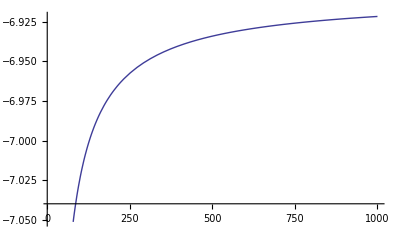

```mathematica
Plot[Log[f[0.001,beta,k]]/k /.beta->1,{k,10,1000}]
```

```mathematica
Limit[Log[f[x,1,k]-f[0,1,k]]/k ,k->Infinity]
```

Log[Tanh[x]]

```mathematica
fbn[beta_, n_]=Assuming[n∈Integers && n>1&&beta >0 ,Integrate[Tanh[beta x]^n,{x,0,1}]]
```

(Hypergeometric2F1[1,(1+n)/2,(3+n)/2,Tanh[beta]^2] Tanh[beta]^(1+n))/(beta+beta n)

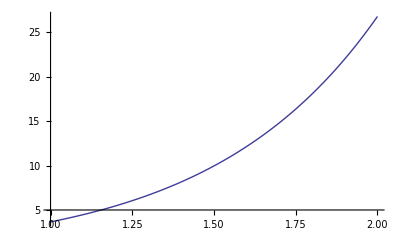

```mathematica
Plot[-1000/Log[fbn[beta,1000]],{beta,1,2}]
```

```mathematica
-1/Log[Tanh[1]]//N
```

3.67186

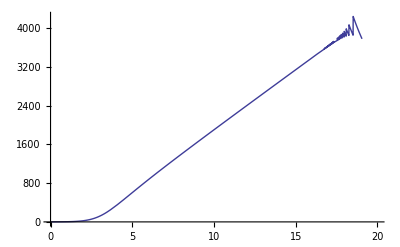

```mathematica
Plot[-1000/Log[fbn[beta,1000]],{beta,0,20}]
```

```mathematica
Limit[k/Log[fbn[beta,k]]/beta,beta->Infinity]
```